```mathematica
temps={36,39,46,56,67,77,82,80,72,62,52,42}
```

{36,39,46,56,67,77,82,80,72,62,52,42}

```mathematica
names={7,8,5,5,3,4,4,6,9,7,8,8}
```

{7,8,5,5,3,4,4,6,9,7,8,8}

```mathematica
RotateRight[temps,3]
```

{62,52,42,36,39,46,56,67,77,82,80,72}

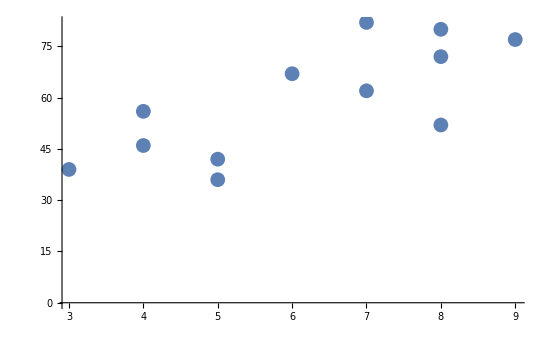

```mathematica
ListPlot[Transpose[{names,%63}]]
```

```mathematica
?PlotLegends
```

PlotLegends is an option for plot functions that specifies what legends to use.

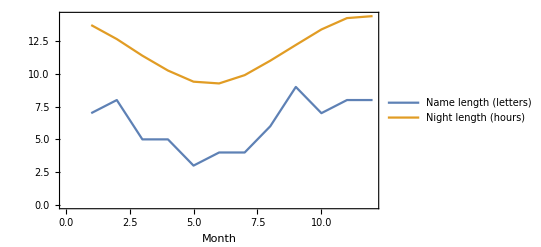

```mathematica
Show[ListLinePlot[{names,nights2},PlotLegends->{"Name length (letters)","Night length (hours)"},Frame->True,FrameLabel->{"Month"}]]
```

```mathematica
?AxesLabel
```

AxesLabel is an option for graphics functions that specifies labels for axes.

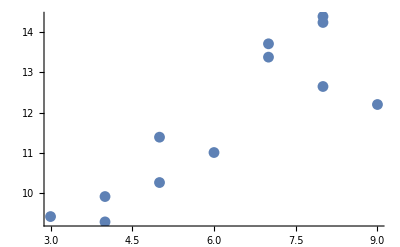

```mathematica
ListPlot[Transpose[{names,nights2}]]
```

```mathematica
Correlation[names,nights2]
```

207 √(6/349435)

```mathematica
N[%]
```

0.857754

```mathematica
Partition[{9,36,10,19,11,24,12,39,13,47,14,37,14,44,14,04,12,58,11,46,10,35,9,44},2]
```

{{9,36},{10,19},{11,24},{12,39},{13,47},{14,37},{14,44},{14,4},{12,58},{11,46},{10,35},{9,44}}

```mathematica
#[[1]]+#[[2]]/60&/@%
```

{48/5,619/60,57/5,253/20,827/60,877/60,221/15,211/15,389/30,353/30,127/12,146/15}

```mathematica
days=%
```

{48/5,619/60,57/5,253/20,827/60,877/60,221/15,211/15,389/30,353/30,127/12,146/15}

```mathematica
nights=24-days
```

{72/5,821/60,63/5,227/20,613/60,563/60,139/15,149/15,331/30,367/30,161/12,214/15}

```mathematica
days2=#[[1]]+#[[2]]/60&/@{{10,17},{11,21},{12,37},{13,45},{14,36},{14,44},{14,6},{13,00},{11,48},{10,37},{9,45},{9,36}}
```

{617/60,227/20,757/60,55/4,73/5,221/15,141/10,13,59/5,637/60,39/4,48/5}

```mathematica
nights2=24-days2
```

{823/60,253/20,683/60,41/4,47/5,139/15,99/10,11,61/5,803/60,57/4,72/5}